```mathematica
γ=267522212; B1=36.39*10^-6; νres=1510; c=0.1;
```

```mathematica
γ=1; B1=1; νres=1; c=0.1;
```

```mathematica
u[ν_]:= 2 π (νres-ν)/(γ B1)
```

```mathematica
MzNorm[Φ0_,ν_]=1/(1+u[ν]^2)(u[ν]^2+Cos[Φ0 √(1+u[ν]^2)]);
```

```mathematica
2*Pi/γ/B1
```

0.000645413

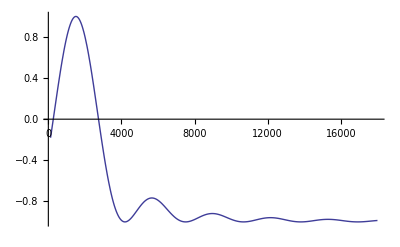

```mathematica
Plot[-MzNorm[Pi,ν],{ν,120,18000},PlotRange->Full]
```

```mathematica
Plot3D[MzNorm[Φ0,ν],{Φ0,0,20},{ν,0,2},ColorFunction->"RustTones", PlotRange->Full,Mesh->None,PlotPoints->50]
```

-Graphics3D-

```mathematica
MzNorm[Φ0_,ν_]:=NIntegrate[1/(1+u[ν]^2)(u[ν]^2+Cos[Φ √(1+u[ν]^2)])*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c Φ0)],{Φ,−100,100}]
```

```mathematica
Plot3D[MzNorm[Φ0,ν],{Φ0,1,20},{ν,0,2},ColorFunction->"RustTones", PlotRange->Full,Mesh->None,PlotPoints->50, AxesLabel->{"Drehwinkel","normierte Frequenz","Signal"},Boxed->False]
```

-Graphics3D-

```mathematica
c=1
```

1

```mathematica
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c Φ0)],{Φ,-10000,10000}]
```

```mathematica
MzNormSpinDreh[5]
```

0.081006

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\kl-Daten.dat", "Table"];
ExData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=Data[[n,1]],{n,1,Length[Data]}]
Print[ExData];
```

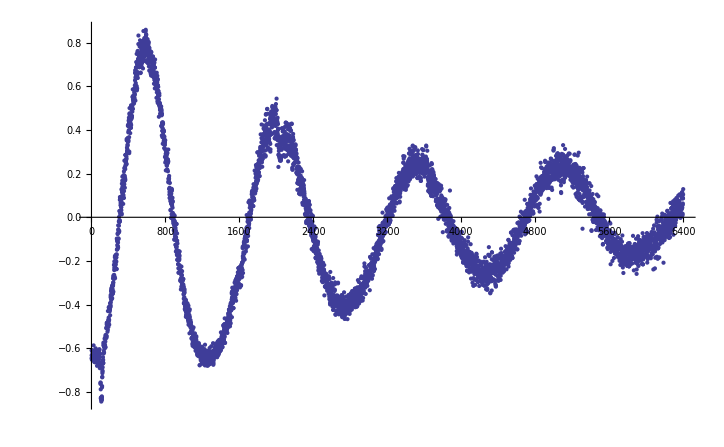

```mathematica
ListPlot[ExData]
```

```mathematica
Manipulate[Plot[-MzNormSpinDreh[Φ*7.845/1700,c],{Φ,0.001,7000}, PlotRange->{-1,1}, PlotPoints->100],{c,0.1,2}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Φ near {Φ} = {0.}. NIntegrate obtained 3.03633 and 0.949044 for the integral and error estimates.

```mathematica
Plot3D[MzNormSpinDreh[Φ],{Φ,1,40},{ν,1,1.3},ColorFunction->"RustTones", PlotRange->Full,Mesh->None,PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot[MzNorm[θ,ν],{θ,0,3*Pi},PlotRange->Full]
```

NIntegrate::inumr: The integrand 128.579\ ⅇ^-51938.7\ (-0.000192535 + Φ)^2\ (4\ π^2\ (1 - ν)^2 + Cos[√1 + 4\ Power[« 2 »]\ Power[« 2 »]\ Φ])/1 + 4\ π^2\ (1 - ν)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-100, 100}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

-Graphics-

```mathematica
Export ["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\Teorie1.dat",
Table[{ν,-MzNorm[Pi,ν]*0.555-0.105},{ν,1200,1800,1}],"Table"]
```

D:\Git\F-Praktikum\NMR\Data-Plots\Teorie1.dat